```mathematica
z=InverseCDF[NormalDistribution[0,1],0.975]
```

1.95996

```mathematica
4938*31/1826-z*Sqrt[(4938*(31^2)/1826*(1/31+1/1826))]
```

65.7353

```mathematica
Data2=Table[4938*i/1826-z*Sqrt[(4938*(i^2)/1826*(1/i+1/1826))],{i,1,110}]
```

{-0.519707,0.847902,2.52566,4.36384,6.30444,8.31773,10.3861,12.4979,14.6454,16.8225,19.025,21.2495,23.4932,25.7539,28.0299,30.3196,32.6217,34.9352,37.2591,39.5926,41.9349,44.2855,46.6438,49.0092,51.3814,53.7598,56.1443,58.5343,60.9297,63.3301,65.7353,68.145,70.5591,72.9774,75.3995,77.8255,80.2551,82.6882,85.1245,87.5642,90.0068,92.4525,94.901,97.3523,99.8062,102.263,104.722,107.183,109.647,112.113,114.581,117.051,119.524,121.998,124.475,126.953,129.433,131.915,134.398,136.883,139.37,141.859,144.349,146.841,149.334,151.828,154.324,156.822,159.321,161.821,164.322,166.825,169.329,171.834,174.34,176.848,179.356,181.866,184.377,186.889,189.402,191.916,194.431,196.947,199.464,201.982,204.501,207.021,209.541,212.063,214.586,217.109,219.633,222.158,224.684,227.211,229.738,232.267,234.796,237.325,239.856,242.387,244.919,247.452,249.985,252.519,255.054,257.59,260.126,262.662}

```mathematica
Data3=Table[4938*i/1826+z*Sqrt[(4938*(i^2)/1826*(1/i+1/1826))],{i,1,110}]
```

{5.92825,9.96918,13.7,17.2703,20.7383,24.1335,27.4737,30.7704,34.0315,37.2629,40.4689,43.653,46.8179,49.9657,53.0982,56.2171,59.3235,62.4186,65.5032,68.5783,71.6445,74.7024,77.7527,80.7958,83.8322,86.8623,89.8864,92.9049,95.9181,98.9262,101.93,104.928,107.923,110.913,113.899,116.882,119.861,122.836,125.809,128.778,131.743,134.706,137.666,140.624,143.578,146.53,149.48,152.427,155.372,158.314,161.255,164.193,167.129,170.063,172.995,175.926,178.854,181.781,184.706,187.629,190.551,193.471,196.389,199.306,202.222,205.135,208.048,210.959,213.869,216.777,219.685,222.59,225.495,228.398,231.301,234.202,237.102,240.,242.898,245.795,248.69,251.585,254.478,257.371,260.262,263.153,266.043,268.931,271.819,274.706,277.592,280.477,283.361,286.245,289.127,292.009,294.89,297.771,300.65,303.529,306.407,309.284,312.161,315.037,317.912,320.786,323.66,326.533,329.406,332.277}

```mathematica
Data1 = {4,10,10,11,17,22,23,25,30,32,35,38,40,41,46,49,50,50,51,55,61,64,70,73,75,75,79,82,85,89,89,93,96,97,101,103,104,107,109,114,117,117,120,124,129,130,134,136,137,138,140,144,145,146,149,157,163,166,167,170,175,177,179,181,184,189,191,197,199,200,202,205,210,216,220,225,225,228,230,234,236,237,238,238,238,238,238,238,238,238,238,238,238,238,238,238,238,238,238,238,238,239,239,240,241,244,246,247,250,251}
```

{4,10,10,11,17,22,23,25,30,32,35,38,40,41,46,49,50,50,51,55,61,64,70,73,75,75,79,82,85,89,89,93,96,97,101,103,104,107,109,114,117,117,120,124,129,130,134,136,137,138,140,144,145,146,149,157,163,166,167,170,175,177,179,181,184,189,191,197,199,200,202,205,210,216,220,225,225,228,230,234,236,237,238,238,238,238,238,238,238,238,238,238,238,238,238,238,238,238,238,238,238,239,239,240,241,244,246,247,250,251}

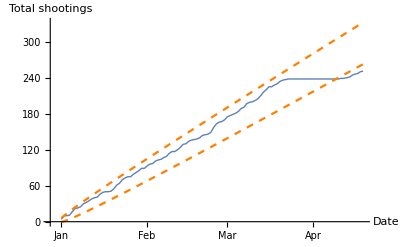

```mathematica
ListLinePlot[{Data1,Data2,Data3},Ticks->{{{1, Jan},{32,Feb},{61,Mar},{92,Apr}},Automatic},PlotStyle->{{Thick},{Orange,Dashed},{Orange,Dashed}},AxesOrigin->{-3,0},AxesLabel->{"Date","Total shootings"}]
```

```mathematica
Length[Data3]
```

110